```mathematica
ϕ=(1+Sqrt[5])/2;
F[x_]:=Sin[x^Cos[x]]^Cos[x]
```

```mathematica
Series[F[x],{x,0,10}]
```

x+(-1/6-Log[x]) x^3+1/120 (11+80 Log[x]+60 Log[x]^2) x^5+((-23-385 Log[x]-840 Log[x]^2-210 Log[x]^3) x^7)/1260+((1829+35544 Log[x]+160776 Log[x]^2+141120 Log[x]^3+15120 Log[x]^4) x^9)/362880+O[x]^11

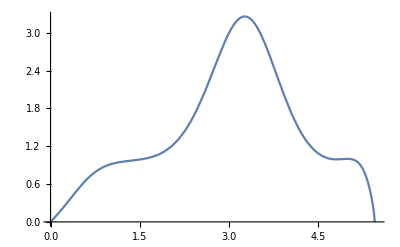

```mathematica
Plot[F[x],{x,0,5.5}]
```

```mathematica
FindRoot[F[x],{x,5.4},WorkingPrecision->30]
```

{x→5.4531894443924405651366541132-2.3921685638669492253325208628×10^-24 ⅈ}

```mathematica
NIntegrate[F[x],{x,0,5.45318944439244056513665411320},WorkingPrecision->15]
```

7.84701478110563

```mathematica
α=2E+Sqrt[(1/2)(-Cos[2π/(1+Sqrt[5])])^(E^2)]
```

2 ⅇ+((-Cos[(2 π)/(1+√5)])^(ⅇ^2/2))/(√2)

```mathematica
N[α,15]
```

5.453189444397

```mathematica
β=2^π-(4-E^(1/ϕ)/2)/π
```

2^π-(4-1/2 ⅇ^(2/(1+√5)))/π

```mathematica
N[β,15]
```

7.84701478110909

```mathematica
NIntegrate[F[x],{x,0,α},WorkingPrecision->15]
```

7.84701478110563